```mathematica
help
```

help

```mathematica
y[x_]:=Sqrt[a*x-x^2]
dy=D[y[x],x];
ds=sqr[1+dy^2];
I1=Integrate[Sqrt[x^2+y[x]]*ds,{x,0,a}]
```

∫_0^a sqr[1+(a-2 x)^2 sqrt'[a x-x^2]^2] √(x^2+sqrt[a x-x^2])ⅆx

```mathematica
Solve[{x+2y==7,x+y==10},{x,y}]
```

{{x→13,y→-3}}

```mathematica
D[x^4,{x,2}]
```

12 x^2

```mathematica
Integrate[2x+3y,{x,1,2},{y,3,5}]
```

30

```mathematica
ParametricPlot3D[{u*Cos[v],u*Sin[v],u^2},{u,-1,2},{v,-Pi,Pi}]
```

-Graphics3D-

```mathematica
z[x_,y_]=x^2+y^2;
dzx=D[z[x,y],x];
dzy=D[z[x,y],y];
ds=z[x,y]*Sqrt[1+dzx^2+dzy^2]/.{x->r*Cos[t],y->r*Sin[t]};
Integrate[ds*r,{t,0,2Pi},{r,0,1/2}]
```

1/60 (1+√2) π

```mathematica
s=a+b;
A=s*(s-a)*(s-b);
A/.{a->1,b->1}
```

2

```mathematica
Solve[{x^2+y^2+z^2==R^2,x+y+z==0},{y,z}]
```

```mathematica
{{y->1/2 (-x-√(2 R^2-3 x^2)),z->1/2 (-x+√(2 R^2-3 x^2))},{y->1/2 (-x+√(2 R^2-3 x^2)),z->1/2 (-x-√(2 R^2-3 x^2))}}
```

```mathematica
dyx=D[y,x];
dzx=D[z,x];
ds=x^2*Sqrt[1+dyx^2+dzx^2];
Integrate[ds,{x,-R,R}]
```

(2 R^3)/3

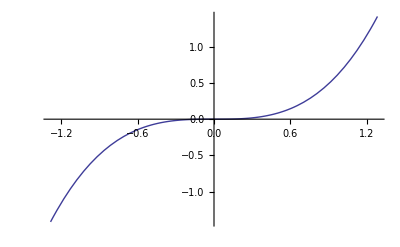

```mathematica
Plot[(2 R^3)/3,{R,-1.2851194708927707,1.2851194708927707}]
```

```mathematica
dyx
```

0

```mathematica
dyx=D[y,x]
```

0

```mathematica
Show[dyx]
```

Show::gtype: Integer 不是一个图形类别.

Show[0]

```mathematica
? Integrate
```

Integrate[f,x] 给出不定积分 ∫f dx. 
Integrate[f,{x,x_min,x_max}] 给出定积分 ∫_x_min^x_max f dx. 
Integrate[f,{x,x_min,x_max},{y,y_min,y_max},…] 给出多重积分 ∫_x_min^x_max dx∫_y_min^y_max dy … f.

```mathematica
1/3
```

1/3

```mathematica
1/3 //N
```

0.333333

```mathematica
N[1/3,50]
```

0.33333333333333333333333333333333333333333333333333

```mathematica
y[x_]:=x^2
```

```mathematica
y[a]
```

a^2

```mathematica
y[1]

? y
```

```mathematica
? y
```

Global`y

y[x]:=sqrt[a x-x^2]
 
y[x_]:=x^2

```mathematica
clear[y]
```

clear[y]

```mathematica
? y
```

Global`y

y[x]:=sqrt[a x-x^2]
 
y[x_]:=x^2

```mathematica
Clear[y]
```

```mathematica
? y
```

Global`y

```mathematica
a=Import["LinearAlgebraExamples/Data/dwt_1005.psa","HarwellBoeing"];
```

```mathematica
GraphPlot3D[a,VertexRenderingFunction->None]
```

-Graphics3D-

```mathematica
Play[Sin[2Pi 440 t],{t,0,1}]
```

-Graphics-

```mathematica
Play[Sin[700 t+25 t Sin[350 t]],{t,0,4}]
```

-Graphics-

```mathematica
{Slider[Dynamic[x]],Dynamic[Plot[Sin[10y x],{y,0,2Pi}]]}
```

{,}

```mathematica
Panel[Column[{Row[{Slider[Dynamic[x]],Dynamic[x]}],Dynamic[Plot[Sin[10y x],{y,0,2Pi}]]}]]
```

```mathematica
DynamicModule[{pt={1,0}},Slider2D[Dynamic[pt,(pt=#/Norm[#])&],{-1,1},Exclusions->{0,0}]]
```

```mathematica
Column[Map[OpenerView[{#,DateListPlot[CountryData[#,{{"GDP"},{1970,2005}}]]}]&,CountryData["GroupOf8"]]]
```

正在从 Wolfram Research 数据服务器安装数据（%）.

```mathematica
TabView[{"Factorial"->40!, "Plot"->Plot[Sin[x],{x,0,2Pi}], "Factor"->Factor[x^14-1]}]
```